```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 2/ohg6-hw2/";
SetDirectory[main];
$Line=0;
```

## Double

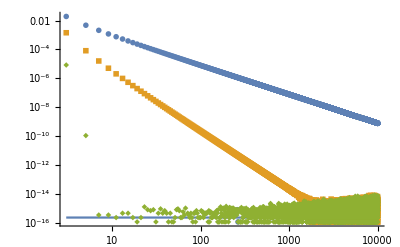

```mathematica
data=Import["double/integdouble.dat"];
plotdata=Table[data[[All,{1,j}]],{j,{2,3,4}}];
Show[LogLogPlot[$MachineEpsilon,{x,data[[1,1]],data[[-1,1]]}],ListLogLogPlot[plotdata,PlotMarkers->{Automatic,Tiny}],PlotRange->All]
```

```mathematica
trapdata=data[[All,{1,2}]];
simpdata=data[[;;1000,{1,3}]];
gaussdata=data[[;;3,{1,4}]];
```

```mathematica
lineartrapfit=LinearModelFit[Log[trapdata],x,x];
lineartrapfit["BestFit"]
linearsimpfit=LinearModelFit[Log[simpdata],x,x];
linearsimpfit["BestFit"]
lineargaussfit=LinearModelFit[Log[gaussdata],x,x];
lineargaussfit["BestFit"]
```

-2.52914-2.00598 x

-3.49661-4.06305 x

19.6167-27.7494 x

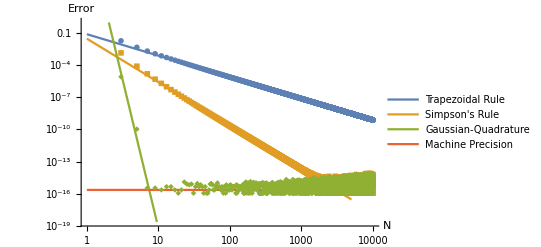

```mathematica
Show[LogLogPlot[{Exp[lineartrapfit["BestFitParameters"][[1]]+lineartrapfit["BestFitParameters"][[2]]*Log[x]],Exp[linearsimpfit["BestFitParameters"][[1]]+linearsimpfit["BestFitParameters"][[2]]*Log[x]],Exp[lineargaussfit["BestFitParameters"][[1]]+lineargaussfit["BestFitParameters"][[2]]*Log[x]],$MachineEpsilon},{x,1,5000},PlotRange->{All,{1,$MachineEpsilon/10^3}},PlotLegends->{"Trapezoidal Rule","Simpson's Rule","Gaussian-Quadrature","Machine Precision"},LabelStyle->{FontFamily->"Times",FontSize->12}],ListLogLogPlot[plotdata,PlotMarkers->{Automatic,Tiny}],AspectRatio->1/GoldenRatio,AxesLabel->{"N","Error"},BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
Export["double/integdouble.png",%]
```

double/integdouble.png

```mathematica
{Exp[Solve[lineartrapfit["BestFit"]==Log[$MachineEpsilon],x][[1,1,2]]],Exp[Solve[linearsimpfit["BestFit"]==Log[$MachineEpsilon],x][[1,1,2]]],Exp[Solve[lineargaussfit["BestFit"]==Log[$MachineEpsilon],x][[1,1,2]]]}
```

{1.80258×10^7,3012.39,7.4322}

```mathematica
{Min[Cases[data[[All,2]],x_/;x≠0]],Min[Cases[data[[All,3]],x_/;x≠0]],Min[Cases[data[[All,4]],x_/;x≠0]]}
```

{7.57749×10^-10,1.11022×10^-16,1.11022×10^-16}

```mathematica
N[(4/($MachineEpsilon))^(2/5)]
1/%^2+√%*$MachineEpsilon
```

3.17869×10^6

4.94851×10^-13

```mathematica
N[(8/($MachineEpsilon))^(2/9)]
N[1/%^4+√%*$MachineEpsilon]
```

4778.1

1.72671×10^-14

```mathematica
1
```

1

## Single

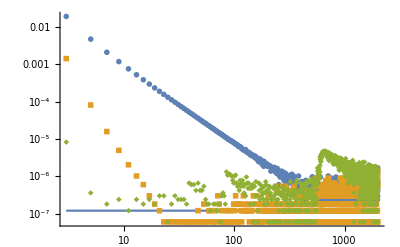

```mathematica
data=Import["single/integsingle.dat"];
plotdata=Table[data[[All,{1,j}]],{j,{2,3,4}}];
Show[LogLogPlot[1.19209290*10^-7,{x,data[[1,1]],data[[-1,1]]}],ListLogLogPlot[plotdata,PlotMarkers->{Automatic,Tiny}],PlotRange->All]
```

```mathematica
trapdata=data[[;;200,{1,2}]];
simpdata=data[[;;10,{1,3}]];
gaussdata=data[[;;2,{1,4}]];
```

```mathematica
lineartrapfit=LinearModelFit[Log[trapdata],x,x];
lineartrapfit["BestFit"]
linearsimpfit=LinearModelFit[Log[simpdata],x,x];
linearsimpfit["BestFit"]
lineargaussfit=LinearModelFit[Log[gaussdata],x,x];
lineargaussfit["BestFit"]
```

-2.24579-2.06097 x

-1.65511-4.73088 x

-4.9649-6.13809 x

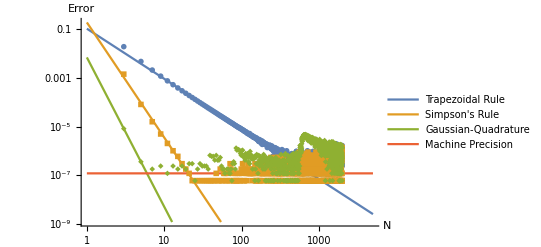

```mathematica
Show[LogLogPlot[{Exp[lineartrapfit["BestFitParameters"][[1]]+lineartrapfit["BestFitParameters"][[2]]*Log[x]],Exp[linearsimpfit["BestFitParameters"][[1]]+linearsimpfit["BestFitParameters"][[2]]*Log[x]],Exp[lineargaussfit["BestFitParameters"][[1]]+lineargaussfit["BestFitParameters"][[2]]*Log[x]],1.19209290*10^-7},{x,1,5000},PlotRange->{All,{1,1.19209290*10^-7/10^2}},PlotLegends->{"Trapezoidal Rule","Simpson's Rule","Gaussian-Quadrature","Machine Precision"},LabelStyle->{FontFamily->"Times",FontSize->12}],ListLogLogPlot[plotdata,PlotMarkers->{Automatic,Tiny}],AspectRatio->1/GoldenRatio,AxesLabel->{"N","Error"},BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
Export["single/integsingle.png",%]
```

single/integsingle.png

```mathematica
{Exp[Solve[lineartrapfit["BestFit"]==Log[$MachineEpsilon],x][[1,1,2]]],Exp[Solve[linearsimpfit["BestFit"]==Log[$MachineEpsilon],x][[1,1,2]]],Exp[Solve[lineargaussfit["BestFit"]==Log[$MachineEpsilon],x][[1,1,2]]]}
```

{1.32434×10^7,1435.05,158.105}

```mathematica
{Min[Cases[data[[All,2]],x_/;x≠0]],Min[Cases[data[[All,3]],x_/;x≠0]],Min[Cases[data[[All,4]],x_/;x≠0]]}
```

{5.96046×10^-8,5.96046×10^-8,5.96046×10^-8}

```mathematica
N[(4/(1.19209290*10^-7))^(2/5)]
N[1/%^2+√%*1.19209290*10^-7]
```

1024.

4.76837×10^-6

```mathematica
N[(8/(1.19209290*10^-7))^(2/9)]
N[1/%^4+√%*1.19209290*10^-7]
```

54.8636

9.93356×10^-7